### Mathematica Hw IV

Claus Ernst/Huanjing Wang		Math/Cs 371 Spring 2016
Due: Wednesday, February 24 before class.  
This assignment must be turned in electronically AND as a hard copy.  The electronic copy must be submitted through blackboard prior to your class.

#### General Requirements - read before you start working

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the code turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 

Each group turns in one (stapled) printout at the beginning of class and submits an electronic copy (one file) prior to class.

Your electronic and hard copy must include: 
a) The names of both group members on the print out (printed from the file, not added by hand). The name of both group members must be included in the name of the electronic file. For example if we (Claus and Huanjing) are a team then the file name should be ErnstWang371Hw4.nb. This will help to identify whose file we are looking at and it will also avoid having several different files with the same name.
b) A solution to each problem, which includes the code, as well as a couple of executions of your code which demonstrate that the code is (most likely) correct. Select different types of input for your example runs, to show that different parts of your code work correctly.   
c) Your solutions must be well-documented Mathematica code, that is, you must use comments, meaningful variable names, proper indentations, hide local variables (if any are needed), etc.  The comments in the code should be such that taken by themselves they describe the algorithm you used.

Note: Throughout this assignment, the lists of arguments for functions maybe given to clarify the order and meaning of the arguments; they do not follow Mathematica syntax. However, your solutions must follow the given order/structure of arguments as specified by the assignment. If you do deviate from this our test programs will not run.

#### 1. The Game of Life

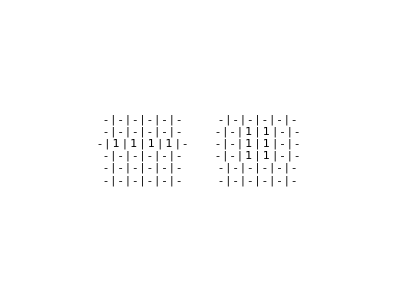
The game of Life was invented by John H. Conway to model some nature laws for birth, death, and survival. Consider a checkerboard consisting of an n-by-n array of squares. Each square can contain one individual (denoted by 1) or be empty (denoted by -). The left figure below shows a 6-by-6 board with four of the squares occupied. The future of each individual depends on the number of its neighbors. After each period of time, called a generation, certain individuals will survive, others will die due to either loneliness or overcrowding, and new individuals will be born. Each nonborder square has eight neighboring squares. After each generation, the status of the squares changes as follows:
(a) An individual survives if there are two or three individuals in neighboring squares.
(b) An individual dies if he has more than three individuals or less than two in neighboring squares.
(c) A new individual is born into each empty square that has exactly three individuals as neighbors.

The right figure below shows the status after one generation.
-Graphics-
Write a complete Mathematica program to perform the following works.
(1) Write a function configurationBoard[n] where n is the size of board, let n is less than 9 and greater than 2. To specify the initial configuration, have the user input each row as a string of length n, and break the row into 1’s or dashes (for example, assume n is 8, a valid input for a row can be “1-11-1-1”) . Then display and return the initial configuration of the board. 

(3) Write a function nextGeneration[currentBoard] where currentBoard is the current generation. This function assigns the next generation values to the current generation, displays and returns the board of next generation.

(4) Write a function multipleGenerations[n, m] where n is the size of the board (n-by-n),m is the number of generations, and m is less than or equal to n. multipleGenerations must call configurationBoard[n] to generate initial configuration. The function then returns the board after m generations. multipleGenerations must call nextGeneration.

Note: If you need helper function, write as many as you need.

Demonstrate that the program works correctly by showing two examples, one of them should be the test case posted in Blakboard. (Hint: the hardest part of the program is determining the number of neighbors a cell has. In general, you must check a 3-by-3 square around the cell in question. Exceptions must be made when the cell is on the edge of the board. Don’t forget that a cell is not a neighbor of itself.)

2. Airline Reservation

Write a reservation system for an airline flight. Assume the airplane has m rows with n seats in each row. Use a table of strings to maintain a seating chart. In addition, create a list to be used as a waiting list in case the plane is full. The waiting list should be “first come, first served”; that is, people who are added early to this list get priority over those added later.

Developing Mathematica code as follows
(1) Write a function initialSeatingChart[m,n] where m is the number of rows and n is the number of seats in each row. This function return an empty seating chart, use dash to represent available seat.

(2) Write a function addSeatingChart[seatingChart, waitingList] where seatingChart is the current seating chart and waitingList is the current waiting list. This function will add a passenger to the flight or waiting list and do the followings:
	Request the passenger’s name.
	Display a chart of seats in the airplane in tabular form.
	If seats are available, let the passenger choose a seat. Add the passenger to the seating chart.
	If no seats are available, place the passenger on the waiting list.
addSeatingChart[seatingChart, waitingList] returns the updated seating chart and waiting list.

(3) Write a function removeSeatingChart[seatingChart, waitingList] where seatingChart is the current seating chart and waitingList is the current waiting list. This function will remove a passenger from the flight and do the followings.
	Request the passenger’s name.
	Search the seating chart for the passenger’s name and delete it.
	If the waiting list is empty, update the seating chart so the seat is available.
	If the waiting list is not empty, remove the first person from the list, and give him or her the newly vacated seat.
removeSeatingChart[seatingChart, waitingList] returns the updated seating chart and waiting list.	

(4) Write a function airlineReservation[m,n] where m is the number of rows and n is the number of seats in each row. This function asks user to perform multiple operations on the reservation system. It first call  the function initialSeatingChart[m,n] and then performs the following repeatedly:
	Display the menu, 1-Add, 2-Remove, 3-Quit
	Ask user to input the operations, the input only can be 1, 2, or 3.
	If user input 1, call addSeatingChart.
	if user input 2, call removeSeatingChart.
	if user input 3, quit the loop
then displays and returns the final seating chart and waiting list.

Demonstrate that the program works correctly by showing two examples, one of them should be the test case posted in Blakboard.